```mathematica
Notebook for the polynomial method in the Schroedinger equation. 
This example is for the case of the hexagonal well of side 1
```

Defining initialization variables

```mathematica
size=15;
L=1;
```

Symbolic integral of the generic x^n y^m integral term

```mathematica
$Assumptions={m≥0&&m∈Integers,n≥0&&n∈Integers,x∈Reals,y∈Reals};
integral[n_,m_]=1/((1+n) (2+m+n))2^(-2-m-n)* 3^((1+m)/2) (1+(-1)^m) (1+(-1)^n) (1+2^(2+m+n) (1+n) Beta[1/2,1+m,1+n]);
AbsoluteTiming[intTablehex=ParallelTable[integral[i,j],{i,0,200},{j,0,200},Method->"CoarsestGrained",DistributedContexts->Automatic];]
MyIntegral[n_,m_]:=MyIntegral[n,m]=intTablehex[[n+1,m+1]]
SetAttributes[MyIntegral,Listable]
AbsoluteTiming[ParallelTable[MyIntegral[i,j],{i,0,199},{j,0,199}];]
```

$Aborted

$Aborted[]

Part::partd: Part specification intTablehex⟦1,2⟧ is longer than depth of object.

Creating data folder

```mathematica
shape="hexagon";
folder="~/agr_tese/data/symbolic_new/schrodinger/"<>shape<>"_";
basissize=ToString[Floor[size]];
CreateDirectory[folder<>basissize]//Quiet;
reg=Polygon[CirclePoints[L,6]];
```

Defining normalization, scalar product, and Hamiltonian integration elements

```mathematica
coeffs[func_]:=coeffs[func]=GroebnerBasis`DistributedTermsList[func,{x,y},MonomialOrder->DegreeLexicographic][[1,All]]
SetAttributes[coeffs,Listable]
MyNorm[func1_]:=√MyProd[func1]

mylist[func1_,func2_]:=coeffs[Flatten[Outer[Times,MonomialList[func1[x,y]],MonomialList[func2[x,y]]]]]
MyProd[func1_]:=Collect[Dot[(Flatten[(func1)[[All,All,2]]]),MyIntegral[(Flatten[(func1)[[All,All,1,1]]]),(Flatten[(func1)[[All,All,1,2]]])]],{x,y},Simplify]

Ham[f1_,f2_]:=(f1[x,y])*(D[f2[x,y],{x,2}]+D[f2[x,y],{y,2}])
En[func1_]:=-1*Inner[Times,(func1[[All,2]]),MyIntegral[func1[[All,1,1]],func1[[All,1,2]]],Plus]
```

Finding the numerical eigenvalues for comparison

```mathematica
exact=(4Tan[π/6])/6*NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈reg,size];
```

```mathematica
(*AbsoluteTiming[Table[CoefficientRules[ϕn[5,x,y]*ϕn[7,x,y]],{i,1,100}];]
AbsoluteTiming[TaExpandble[CoefficientRules[Simplify[ϕn[5,x,y]*ϕn[7,x,y]]],{i,1,100}];]
AbsoluteTiming[Table[CoefficientRules[Expand[ϕn[5,x,y]*ϕn[7,x,y]]],{i,1,100}];]*)
```

Defining the initial function

```mathematica
ϕu[1,x_,y_]=(y-(√3)/2 L)*(y+(√3)/2 L)*(x-(√3)/3 y-L)*(x-(√3)/3 y+L)*(x+(√3)/3 y-L)*(x+(√3)/3 y+L);
ϕn[1,x_,y_]=Expand[Simplify[(1/(MyNorm[mylist[ϕu[1,#1,#2]&,ϕu[1,#1,#2]&]]))*ϕu[1,x,y]]];
En[coeffs[N[Ham[ϕn[1,#1,#2]&,ϕn[1,#1,#2]&]]]]//AbsoluteTiming
```

{0.006438,7.26185}

```mathematica
AbsoluteTiming[CoefficientRules[ϕn[1,x,y],{x,y}];]
AbsoluteTiming[AAA=GroebnerBasis`DistributedTermsList[ϕn[1,x,y],{x,y},MonomialOrder->DegreeLexicographic][[1,All]];]
```

{0.006889,Null}

{0.001134,Null}

```mathematica
f[m_,x_,y_]:=If[Mod[(m-1)-(Floor[√(m-1)])^2,2]==0,x^Floor[√(m-1)]*y^(((m-1)-(Floor[√(m-1)])^2)/2),x^(((m-1)-(Floor[√(m-1)])^2-1)/2)*y^Floor[√(m-1)]]
Basis[x_,y_]={ϕn[1,x,y]};
For[counter=2,counter<37,counter++,ϕun[counter,x_,y_]=Expand[f[counter,x,y]*ϕn[1,x,y]];
ϕu[counter,x_,y_]=Expand[ϕun[counter,x,y]-Dot[ParallelTable[MyProd[mylist[ϕun[counter,#1,#2]&,ϕn[n,#1,#2]&]],{n,1,counter-1},Method->"CoarsestGrained"],Basis[x,y]]];
ϕn[counter,x_,y_]=Expand[ϕu[counter,x,y]/MyNorm[mylist[ϕu[counter,#1,#2]&,ϕu[counter,#1,#2]&]],Simplify];AppendTo[Basis[x,y],ϕn[counter,x,y]];
Print[counter]]//AbsoluteTiming
Length[Basis[x,y]]
```

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

{143.675,Null}

36

Uncomment this table for verification of the orthogonality of the basis

```mathematica
(*ortho=ParallelTable[MyProd[Basis[#1,#2][[b]]&,Basis[#1,#2][[c]]&],{b,1,size},{c,1,i},Method->"FinestGrained",DistributedContexts->Automatic];//AbsoluteTiming
orthofull=MapThread[Join,{ortho,Rest/@Flatten[Conjugate[ortho],{{2},{1}}]}];]
MatrixForm[orthofull]//Chop*)
```

Calculate the Hamiltonian matrix
It is Hermitian, so only the upper-triangular matrix is calculated

```mathematica
AbsoluteTiming[H=ParallelTable[Ham[Basis[#1,#2][[i]]&,Basis[#1,#2][[j]]&],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
AbsoluteTiming[Hn=ParallelTable[coeffs[N[H[[i,j]],100]],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
AbsoluteTiming[H2=ParallelTable[En[Hn[[i,j]]],{i,1,size},{j,1,i},Method->"FinestGrained",DistributedContexts->Automatic];]
AbsoluteTiming[Hfull=MapThread[Join,{H2,Rest/@Flatten[Conjugate[H2],{{2},{1}}]}];]
MatrixForm[Hfull]
```

{4.71601,Null}

{16.6454,Null}

{5.36191,Null}

{0.000538,Null}

(7.2618461214609 | 0 | 0 | 0 | -1.083051162822 | -1.196375442328 | 0 | 0 | -0.627748395765 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.09148857124 | -1.07201472552 | 0 | 0 | -0.12208360755 | -0.684321569287 | 0 | 0 | -0.19151941315 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.816790173902 | -0.744270883603 | 0 | 0 | -0.20229702312 | -0.53712737227 | 0 | 0 | -0.1260595755
0 | 18.191310245507 | 0 | 0 | 0 | 0 | 0 | 0.275311418023 | 0 | 0.588567029751 | 0 | 0 | 0 | 0.80638637175 | 0 | 0 | 0 | 0 | 0 | -1.03558204533 | 0 | 0 | 0 | -0.6847171167 | 0 | -1.1371883113 | 0 | 0 | 0 | 0.62939111829 | 0 | 0 | 0 | -0.0477269 | 0 | 0 | 0 | 0 | 0 | -0.96279524705 | 0 | 0 | 0 | -0.6598047947 | 0
0 | 0 | 18.191310245507 | 0 | 0 | 0 | 0.287243849601 | 0 | 0 | 0 | 0.582836594828 | 0 | 0 | 0 | -1.61693204521 | 0 | 0 | 0 | 0.06064526225 | 0 | 0 | 0 | 0.05673262575 | 0 | 0 | 0 | -0.70272508682 | 0 | 0 | 0 | -1.7328102536 | 0 | 0 | 0 | -0.3214764985 | 0 | 0 | 0 | 0.06683266516 | 0 | 0 | 0 | -0.1523765434 | 0 | 0
0 | 0 | 0 | 33.035888235359 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.30609933916 | 2.6173397807 | 0 | 0 | 0.2265354175 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.7853195439 | -1.5298606076 | 0 | 0 | 1.6689604171 | -1.206372248 | 0 | 0 | 0.167048293 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.083051162822 | 0 | 0 | 0 | 35.5759384049 | 2.80582649226 | 0 | 0 | 3.83282730569 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.07919877695 | 0.36576002819 | 0 | 0 | 4.43137679641 | 0.4558802019 | 0 | 0 | -0.4972476293 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.548890856 | 0.00546768603 | 0 | 0 | 3.7666524713 | -0.4144313841 | 0 | 0 | 0.219388199
-1.196375442328 | 0 | 0 | 0 | 2.80582649226 | 36.13530036472 | 0 | 0 | 0.88272069359 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.06447299405 | 7.10169580979 | 0 | 0 | 2.6005365668 | -2.6154262437 | 0 | 0 | 0.255813309 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.0687562474 | 2.7587199497 | 0 | 0 | 1.527600041 | -3.333912169 | 0 | 0 | 0.4485228543
0 | 0 | 0.287243849601 | 0 | 0 | 0 | 57.64503914731 | 0 | 0 | 0 | 3.85409576215 | 0 | 0 | 0 | 5.19294294821 | 0 | 0 | 0 | 17.7808286344 | 0 | 0 | 0 | 5.321448664 | 0 | 0 | 0 | 0.1773340196 | 0 | 0 | 0 | 0.001719624 | 0 | 0 | 0 | -0.8321205962 | 0 | 0 | 0 | 9.6028042779 | 0 | 0 | 0 | 5.336804699 | 0 | 0
0 | 0.275311418023 | 0 | 0 | 0 | 0 | 0 | 51.5378687296 | 0 | 6.51475099541 | 0 | 0 | 0 | 7.34143794823 | 0 | 0 | 0 | 0 | 0 | 7.84657081137 | 0 | 0 | 0 | -1.305704453 | 0 | 4.091291589 | 0 | 0 | 0 | 5.1369795838 | 0 | 0 | 0 | 3.123759319 | 0 | 0 | 0 | 0 | 0 | 0.229368528 | 0 | 0 | 0 | -3.115627942 | 0
-0.627748395765 | 0 | 0 | 0 | 3.83282730569 | 0.88272069359 | 0 | 0 | 79.70123137562 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.9130513495 | 3.3343582019 | 0 | 0 | 19.289905767 | 18.169247982 | 0 | 0 | 5.327096378 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.5582277668 | -1.359892942 | 0 | 0 | 14.29815138 | 2.29784968 | 0 | 0 | 8.254565174
0 | 0.588567029751 | 0 | 0 | 0 | 0 | 0 | 6.51475099541 | 0 | 62.41787552057 | 0 | 0 | 0 | 10.1449668978 | 0 | 0 | 0 | 0 | 0 | 2.6180632037 | 0 | 0 | 0 | -1.849517903 | 0 | 17.334745075 | 0 | 0 | 0 | 11.348062233 | 0 | 0 | 0 | -0.123689695 | 0 | 0 | 0 | 0 | 0 | 0.5472298784 | 0 | 0 | 0 | -1.50491097 | 0
0 | 0 | 0.582836594828 | 0 | 0 | 0 | 3.85409576215 | 0 | 0 | 0 | 63.56580831062 | 0 | 0 | 0 | 0.147602743 | 0 | 0 | 0 | 3.9477256324 | 0 | 0 | 0 | 3.5783134111 | 0 | 0 | 0 | 21.036777773 | 0 | 0 | 0 | -4.760067515 | 0 | 0 | 0 | 0.322855141 | 0 | 0 | 0 | 2.369443947 | 0 | 0 | 0 | 2.529463819 | 0 | 0
0 | 0 | 0 | 5.30609933916 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 91.43871661803 | 13.1918827257 | 0 | 0 | 10.750781685 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 37.112463712 | 2.44929064 | 0 | 0 | 13.016410525 | 3.695018269 | 0 | 0 | -0.080022153 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2.6173397807 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.1918827257 | 83.4362941667 | 0 | 0 | 10.283958316 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.144952062 | 19.991474036 | 0 | 0 | 12.407651244 | 0.636839595 | 0 | 0 | 4.45976323 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.80638637175 | 0 | 0 | 0 | 0 | 0 | 7.34143794823 | 0 | 10.1449668978 | 0 | 0 | 0 | 118.663044541 | 0 | 0 | 0 | 0 | 0 | 14.673523105 | 0 | 0 | 0 | 14.995266211 | 0 | 18.580876663 | 0 | 0 | 0 | 49.638134784 | 0 | 0 | 0 | 15.02573433 | 0 | 0 | 0 | 0 | 0 | 2.952021968 | 0 | 0 | 0 | 5.14536512 | 0
0 | 0 | -1.61693204521 | 0 | 0 | 0 | 5.19294294821 | 0 | 0 | 0 | 0.147602743 | 0 | 0 | 0 | 107.044131725 | 0 | 0 | 0 | 16.123198598 | 0 | 0 | 0 | 21.118601475 | 0 | 0 | 0 | 2.481755722 | 0 | 0 | 0 | 28.501689142 | 0 | 0 | 0 | 2.62612088 | 0 | 0 | 0 | 7.968098058 | 0 | 0 | 0 | 18.38974004 | 0 | 0
0 | 0 | 0 | 0.2265354175 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.750781685 | 10.283958316 | 0 | 0 | 149.46026229 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24.00894055 | 14.42733653 | 0 | 0 | 39.08792473 | 50.78471026 | 0 | 0 | 14.0535993 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.09148857124 | 0 | 0 | 0 | 6.07919877695 | 2.06447299405 | 0 | 0 | 11.9130513495 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 98.2110594867 | 1.0653991139 | 0 | 0 | 19.031927751 | 6.0799592764 | 0 | 0 | -2.193815779 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 34.851139245 | -0.4644992929 | 0 | 0 | 21.90823868 | 1.62399842 | 0 | 0 | 0.355151318
-1.07201472552 | 0 | 0 | 0 | 0.36576002819 | 7.10169580979 | 0 | 0 | 3.3343582019 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.0653991139 | 103.071729639 | 0 | 0 | 5.8739149331 | 0.416375642 | 0 | 0 | 4.321491931 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.8476024321 | 44.568381776 | 0 | 0 | 4.787163521 | -7.57014364 | 0 | 0 | 2.81583702
0 | 0 | 0.06064526225 | 0 | 0 | 0 | 17.7808286344 | 0 | 0 | 0 | 3.9477256324 | 0 | 0 | 0 | 16.123198598 | 0 | 0 | 0 | 150.19629573 | 0 | 0 | 0 | 24.600128378 | 0 | 0 | 0 | 2.969073552 | 0 | 0 | 0 | 10.1169905 | 0 | 0 | 0 | -1.33647686 | 0 | 0 | 0 | 72.365628969 | 0 | 0 | 0 | 30.29922919 | 0 | 0
0 | -1.03558204533 | 0 | 0 | 0 | 0 | 0 | 7.84657081137 | 0 | 2.6180632037 | 0 | 0 | 0 | 14.673523105 | 0 | 0 | 0 | 0 | 0 | 122.390962849 | 0 | 0 | 0 | 8.815900899 | 0 | 3.40702226 | 0 | 0 | 0 | 17.44489257 | 0 | 0 | 0 | 13.72984858 | 0 | 0 | 0 | 0 | 0 | 41.221598294 | 0 | 0 | 0 | -3.00792686 | 0
-0.12208360755 | 0 | 0 | 0 | 4.43137679641 | 2.6005365668 | 0 | 0 | 19.289905767 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.031927751 | 5.8739149331 | 0 | 0 | 166.424164622 | 31.898224101 | 0 | 0 | 19.96590374 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27.91394576 | 3.556860927 | 0 | 0 | 81.79412347 | 6.73562673 | 0 | 0 | 27.77114679
-0.684321569287 | 0 | 0 | 0 | 0.4558802019 | -2.6154262437 | 0 | 0 | 18.169247982 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.0799592764 | 0.416375642 | 0 | 0 | 31.898224101 | 167.0737435 | 0 | 0 | 30.35984107 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.167396675 | 0.46318069 | 0 | 0 | 39.78776427 | 52.96316565 | 0 | 0 | 32.89004854
0 | 0 | 0.05673262575 | 0 | 0 | 0 | 5.321448664 | 0 | 0 | 0 | 3.5783134111 | 0 | 0 | 0 | 21.118601475 | 0 | 0 | 0 | 24.600128378 | 0 | 0 | 0 | 200.60801209 | 0 | 0 | 0 | 11.03964154 | 0 | 0 | 0 | 32.97561028 | 0 | 0 | 0 | 25.7467027 | 0 | 0 | 0 | 33.01925342 | 0 | 0 | 0 | 98.02549483 | 0 | 0
0 | -0.6847171167 | 0 | 0 | 0 | 0 | 0 | -1.305704453 | 0 | -1.849517903 | 0 | 0 | 0 | 14.995266211 | 0 | 0 | 0 | 0 | 0 | 8.815900899 | 0 | 0 | 0 | 185.67043773 | 0 | -8.216668086 | 0 | 0 | 0 | 31.49888442 | 0 | 0 | 0 | 36.88968289 | 0 | 0 | 0 | 0 | 0 | 14.6531224 | 0 | 0 | 0 | 66.6043086 | 0
-0.19151941315 | 0 | 0 | 0 | -0.4972476293 | 0.255813309 | 0 | 0 | 5.327096378 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.193815779 | 4.321491931 | 0 | 0 | 19.96590374 | 30.35984107 | 0 | 0 | 238.8752996 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -11.873661 | 12.0787935 | 0 | 0 | 40.5660882 | 35.1327994 | 0 | 0 | 60.4619074
0 | -1.1371883113 | 0 | 0 | 0 | 0 | 0 | 4.091291589 | 0 | 17.334745075 | 0 | 0 | 0 | 18.580876663 | 0 | 0 | 0 | 0 | 0 | 3.40702226 | 0 | 0 | 0 | -8.216668086 | 0 | 145.71259294 | 0 | 0 | 0 | 30.58430772 | 0 | 0 | 0 | -4.52832931 | 0 | 0 | 0 | 0 | 0 | 0.46454447 | 0 | 0 | 0 | -4.96253817 | 0
0 | 0 | -0.70272508682 | 0 | 0 | 0 | 0.1773340196 | 0 | 0 | 0 | 21.036777773 | 0 | 0 | 0 | 2.481755722 | 0 | 0 | 0 | 2.969073552 | 0 | 0 | 0 | 11.03964154 | 0 | 0 | 0 | 158.48175182 | 0 | 0 | 0 | -0.19279447 | 0 | 0 | 0 | 5.7431215 | 0 | 0 | 0 | 3.59224525 | 0 | 0 | 0 | 9.53726345 | 0 | 0
0 | 0 | 0 | 2.7853195439 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 37.112463712 | 13.144952062 | 0 | 0 | 24.00894055 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 217.96542023 | 7.89447919 | 0 | 0 | 39.62830827 | 17.7678541 | 0 | 0 | -0.04487766 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1.5298606076 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.44929064 | 19.991474036 | 0 | 0 | 14.42733653 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.89447919 | 174.52799677 | 0 | 0 | 16.89891554 | 15.7084389 | 0 | 0 | 15.595489 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.62939111829 | 0 | 0 | 0 | 0 | 0 | 5.1369795838 | 0 | 11.348062233 | 0 | 0 | 0 | 49.638134784 | 0 | 0 | 0 | 0 | 0 | 17.44489257 | 0 | 0 | 0 | 31.49888442 | 0 | 30.58430772 | 0 | 0 | 0 | 272.30498134 | 0 | 0 | 0 | 48.64265386 | 0 | 0 | 0 | 0 | 0 | 14.65731 | 0 | 0 | 0 | 27.4501864 | 0
0 | 0 | -1.7328102536 | 0 | 0 | 0 | 0.001719624 | 0 | 0 | 0 | -4.760067515 | 0 | 0 | 0 | 28.501689142 | 0 | 0 | 0 | 10.1169905 | 0 | 0 | 0 | 32.97561028 | 0 | 0 | 0 | -0.19279447 | 0 | 0 | 0 | 220.0552365 | 0 | 0 | 0 | 27.3499258 | 0 | 0 | 0 | 8.97951966 | 0 | 0 | 0 | 46.9577557 | 0 | 0
0 | 0 | 0 | 1.6689604171 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.016410525 | 12.407651244 | 0 | 0 | 39.08792473 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 39.62830827 | 16.89891554 | 0 | 0 | 262.5332003 | 56.1330886 | 0 | 0 | 27.0158296 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1.206372248 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.695018269 | 0.636839595 | 0 | 0 | 50.78471026 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 17.7678541 | 15.7084389 | 0 | 0 | 56.1330886 | 296.7309341 | 0 | 0 | 57.3436913 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.0477269 | 0 | 0 | 0 | 0 | 0 | 3.123759319 | 0 | -0.123689695 | 0 | 0 | 0 | 15.02573433 | 0 | 0 | 0 | 0 | 0 | 13.72984858 | 0 | 0 | 0 | 36.88968289 | 0 | -4.52832931 | 0 | 0 | 0 | 48.64265386 | 0 | 0 | 0 | 298.7922512 | 0 | 0 | 0 | 0 | 0 | 29.6546645 | 0 | 0 | 0 | 51.9227589 | 0
0 | 0 | -0.3214764985 | 0 | 0 | 0 | -0.8321205962 | 0 | 0 | 0 | 0.322855141 | 0 | 0 | 0 | 2.62612088 | 0 | 0 | 0 | -1.33647686 | 0 | 0 | 0 | 25.7467027 | 0 | 0 | 0 | 5.7431215 | 0 | 0 | 0 | 27.3499258 | 0 | 0 | 0 | 285.176648 | 0 | 0 | 0 | -12.5564146 | 0 | 0 | 0 | 49.4804578 | 0 | 0
0 | 0 | 0 | 0.167048293 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.080022153 | 4.45976323 | 0 | 0 | 14.0535993 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.04487766 | 15.595489 | 0 | 0 | 27.0158296 | 57.3436913 | 0 | 0 | 346.061967 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.816790173902 | 0 | 0 | 0 | 0.548890856 | 1.0687562474 | 0 | 0 | 7.5582277668 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 34.851139245 | 0.8476024321 | 0 | 0 | 27.91394576 | 7.167396675 | 0 | 0 | -11.873661 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 205.00006249 | -0.969789191 | 0 | 0 | 45.78116186 | 1.8338692 | 0 | 0 | -5.77772663
-0.744270883603 | 0 | 0 | 0 | 0.00546768603 | 2.7587199497 | 0 | 0 | -1.359892942 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.4644992929 | 44.568381776 | 0 | 0 | 3.556860927 | 0.46318069 | 0 | 0 | 12.0787935 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.969789191 | 230.59437467 | 0 | 0 | 6.18056481 | -3.3342654 | 0 | 0 | 4.67586601
0 | 0 | 0.06683266516 | 0 | 0 | 0 | 9.6028042779 | 0 | 0 | 0 | 2.369443947 | 0 | 0 | 0 | 7.968098058 | 0 | 0 | 0 | 72.365628969 | 0 | 0 | 0 | 33.01925342 | 0 | 0 | 0 | 3.59224525 | 0 | 0 | 0 | 8.97951966 | 0 | 0 | 0 | -12.5564146 | 0 | 0 | 0 | 307.4069917 | 0 | 0 | 0 | 60.3004389 | 0 | 0
0 | -0.96279524705 | 0 | 0 | 0 | 0 | 0 | 0.229368528 | 0 | 0.5472298784 | 0 | 0 | 0 | 2.952021968 | 0 | 0 | 0 | 0 | 0 | 41.221598294 | 0 | 0 | 0 | 14.6531224 | 0 | 0.46454447 | 0 | 0 | 0 | 14.65731 | 0 | 0 | 0 | 29.6546645 | 0 | 0 | 0 | 0 | 0 | 247.4746362 | 0 | 0 | 0 | 17.4522496 | 0
-0.20229702312 | 0 | 0 | 0 | 3.7666524713 | 1.527600041 | 0 | 0 | 14.29815138 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21.90823868 | 4.787163521 | 0 | 0 | 81.79412347 | 39.78776427 | 0 | 0 | 40.5660882 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45.78116186 | 6.18056481 | 0 | 0 | 369.9582832 | 26.1217002 | 0 | 0 | 72.4468929
-0.53712737227 | 0 | 0 | 0 | -0.4144313841 | -3.333912169 | 0 | 0 | 2.29784968 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.62399842 | -7.57014364 | 0 | 0 | 6.73562673 | 52.96316565 | 0 | 0 | 35.1327994 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.8338692 | -3.3342654 | 0 | 0 | 26.1217002 | 290.7408688 | 0 | 0 | 34.6786767
0 | 0 | -0.1523765434 | 0 | 0 | 0 | 5.336804699 | 0 | 0 | 0 | 2.529463819 | 0 | 0 | 0 | 18.38974004 | 0 | 0 | 0 | 30.29922919 | 0 | 0 | 0 | 98.02549483 | 0 | 0 | 0 | 9.53726345 | 0 | 0 | 0 | 46.9577557 | 0 | 0 | 0 | 49.4804578 | 0 | 0 | 0 | 60.3004389 | 0 | 0 | 0 | 438.004535 | 0 | 0
0 | -0.6598047947 | 0 | 0 | 0 | 0 | 0 | -3.115627942 | 0 | -1.50491097 | 0 | 0 | 0 | 5.14536512 | 0 | 0 | 0 | 0 | 0 | -3.00792686 | 0 | 0 | 0 | 66.6043086 | 0 | -4.96253817 | 0 | 0 | 0 | 27.4501864 | 0 | 0 | 0 | 51.9227589 | 0 | 0 | 0 | 0 | 0 | 17.4522496 | 0 | 0 | 0 | 364.367012 | 0
-0.1260595755 | 0 | 0 | 0 | 0.219388199 | 0.4485228543 | 0 | 0 | 8.254565174 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.355151318 | 2.81583702 | 0 | 0 | 27.77114679 | 32.89004854 | 0 | 0 | 60.4619074 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.77772663 | 4.67586601 | 0 | 0 | 72.4468929 | 34.6786767 | 0 | 0 | 378.792704)

Obtaining the numerical eigenvalues and eigenvectors

```mathematica
eval=Eigenvalues[Hfull];//AbsoluteTiming
evec=Eigenvectors[Hfull];
```

{0.073461,Null}

Plotting the eigenvalues

{2.900483,7.350312,7.351213,13.15558,13.15566,15.19807,19.32451,21.34152,24.4168,24.45279,28.47216,28.50225,35.70098,35.78184,36.78562,38.43622,38.67461,46.05999,49.68945,50.72325,51.56796,55.76504,62.25821,63.288,66.16262,68.89914,70.72016,77.04205,79.6751,86.5631,87.01473,95.05465,96.62347,100.4546,103.4781,104.3127,118.3208,123.6239,125.1487,132.6053,135.6924,172.8228,181.9432,212.3451,215.7953}

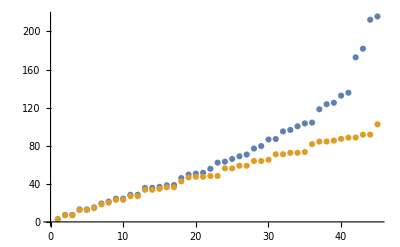

```mathematica
Sort[Abs[eval]/(π^2/4)]
ListPlot[{Sort[Abs[eval]/(π^2/4)],exact}]
```

Defining the eigenbasis

```mathematica
For[i=1,i<size+1,i++,
mode[i,x_,y_]=(evec[[i]]).Basis[x,y];
Print[i]]//AbsoluteTiming
BasisN[x_,y_]=Table[mode[aa,x,y],{aa,1,size}];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

{0.069941,Null}

Comparing eigenvalues

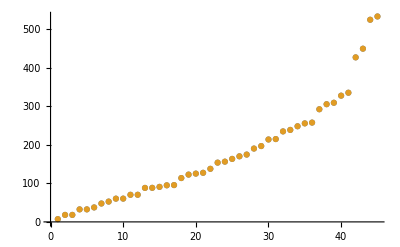

```mathematica
AAAA=Sort[Table[(Conjugate[evec].Hfull.Transpose[evec])[[i,i]],{i,1,size}]];
ListPlot[{AAAA,Sort[Re[Abs[eval]]]}]
```

Exporting the data

```mathematica
Export[folder<>basissize<>"/eigenvalues.dat",Append[Sort[Re[Abs[eval]]],]]
Export[folder<>basissize<>"/basis.m",Basis[x,y]]
Export[folder<>basissize<>"/eigenvectors.m",evec]
Export[folder<>basissize<>"/full_hamiltonian.m",Hfull]
Export[folder<>basissize<>"/eigenfunctions.m",Table[mode[aa,x,y],{aa,1,size}]]
```

~/agr_tese/data/symbolic_new/schrodinger/hexagon_45/eigenvalues.dat

~/agr_tese/data/symbolic_new/schrodinger/hexagon_45/basis.m

~/agr_tese/data/symbolic_new/schrodinger/hexagon_45/eigenvectors.m

~/agr_tese/data/symbolic_new/schrodinger/hexagon_45/full_hamiltonian.m

~/agr_tese/data/symbolic_new/schrodinger/hexagon_45/eigenfunctions.m

Plotting the eigenfunctions

```mathematica
(*ParallelTable[{Plot3D[BasisN[x,y][[aa]],{x,y}∈reg,ImageSize->Large],DensityPlot[Abs[BasisN[x,y][[aa]]]^2,{x,y}∈reg,ImageSize->Large,ColorFunction->"SunsetColors",PlotPoints->100]},{aa,size,1,-1},Method->"CoarsestGrained",DistributedContexts->Automatic]//AbsoluteTiming*)
```